# Neural Networks and Audio

## EPFL, Lausanne, Switzerland 6^thof December 2022

Markus van Almsick, Wolfram Research Inc.

-Graphics-

## Learning Objectives

This talk introduces you to the basics of neural networks acting of audio data.

## Outline

## • Audio Data

## • Human Auditory System

## • Audio NetEncoders

## • Convolutional Neural Networks

## • Recurrent Neural Networks

## • Transfer Learning

## Audio Data

## Audio

Some audio samples:

```mathematica
audio1
```

```mathematica
audio2
```

```mathematica
audio3
```

```mathematica
audio4
```

## Audio Representation

```mathematica
DynamicModule[
{audio=audio3,
d=QuantityMagnitude[Duration[audio3],"s"]},
Manipulate[
AudioPlot[audio,PlotRange->{start,start+zoom},ImageSize->Large],
{{start,0.145},0,d-zoom},{{zoom,0.025},0.01,d}
]
]
```

## Frequency Representation

For simplicity we reduce a stereo to a mono audio signal:

```mathematica
mono3 = AudioChannelMix[audio3,"Mono"];
```

The (Fast-) Fourier transformation provides the audio spectrum denoting the amplitude of each frequency in the signal.

```mathematica
ListLinePlot[
Abs@Fourier[First@AudioData@mono3],
PlotRange->All,ImageSize->Large
]
```

Due to the fact that the audio is a real-values signal, the discrete Fast Fourier transform is symmetric. 
We only consider the right half of the spectrum.

## Log Frequency Representation

Human do not percieve the loudness of an audio signal in a linear but rather in a logarithmic fashion.
Taking the log base 10 of the square amplitudes gives you the power spectrum in dezible [dB].

```mathematica
ListLinePlot[
Take[
20Log[10,Abs@Fourier[First@AudioData@mono3]],
Ceiling[QuantityMagnitude@AudioLength[mono3]/2]
],
PlotRange->All,ImageSize->Large
]
```

The Periodogrampaclet:ref/Periodogram does exactly that:

```mathematica
Periodogram[mono3,ImageSize->Large]
```

Partitioning the audio sequence into overlapping time-windows let’s you observe the dynamic of a power spectrum over time.

```mathematica
ts=
AudioBlockMap[
Periodogram[#,PlotRange->{-120,0},ImageSize->Large]&,
mono3,
{Quantity[64, "Milliseconds"], Quantity[32, "Milliseconds"]}
];
```

```mathematica
ListAnimate[Values[ts]]
```

## Spectrogram

Spectrogrampaclet:ref/Spectrogram plots the magnitude of the short-time Fourier transform (STFT), computed as a discrete Fourier transform (DFT) of partitions of data.

```mathematica
Spectrogram[audio3,ImageSize->Large,PlotRange->"Music"]
```

Spectrogrampaclet:ref/Spectrogram[list] uses partitions of length n=2^Round[log_2(√m)+1] and offset d=Round[n/3], where m is Lengthpaclet:ref/Length[list].

Using shorter partitions increases temporal resolution and decreases frequency resolution.

```mathematica
Spectrogram[audio3,256,85,HannWindow,ImageSize->Large,PlotRange->"Music"]
```

Using longer partitions decreases temporal resolution and increases frequency resolution.

```mathematica
Spectrogram[audio3,2048,683,HannWindow,ImageSize->Large,PlotRange->"Music"]
```

## MEL-Spectrogram

The MEL spectrogram uses a logarithmic frequency scale to mimic the human frequency resolution.

```mathematica
Spectrogram[audio3,ImageSize->Large,Method->"MelFrequency"]
```

```mathematica
SinNote=f↦AudioPad[AudioGenerator[{"Sin",f},1/8],{1/32,1/32},"Faded"];
```

### Linear Frequency Scale

Listen to the scale of linearly increasing frequencies. Note, that the steps in pitch appear to get smaller.

```mathematica
notes=NestList[#+21.802166666666665&,2 130.813,36]
```

```mathematica
BarChart[notes,AxesLabel->{"t","f"}]
```

```mathematica
scale=AudioJoin@Map[SinNote,notes]
```

```mathematica
Spectrogram[scale,ImageSize->Large, PlotRange->{0,1600},
Epilog-> {Green,Thick,Line[{Scaled[{0,0.16}],Scaled[{1,0.66}]}]},
FrameLabel->{"t [s]","frequency f [Hz]"}]
```

### Exponential Frequency Scale

The human auditory system is more sensitive to changes in low than in high frequencies.

```mathematica
notes=NestList[2^(1/12)#&,2 130.813,36];
```

```mathematica
BarChart[notes,AxesLabel->{"t [s]","f [Hz]"},ImageSize->640,LabelStyle->Directive[FontSize->18]]
```

```mathematica
scale=AudioJoin@Map[SinNote,notes]
```

```mathematica
Spectrogram[scale,ImageSize->Large, PlotRange->{0,2400},ImageSize->640,
Epilog-> {Green,Thick,Line@Table[Scaled[{k/3,2^k/9}],{k,0,3,1/7}]},
FrameLabel->{"t [s]","frequency f [Hz]"},LabelStyle->Directive[FontSize->18]]
```

The Mel-spectogram is based on a log-scale binnning of frequency, thereby mimicing human audio perception.

```mathematica
Spectrogram[scale,ImageSize->Large, PlotRange->{1,12000},Method->"MelFrequency",
ImageSize->640,Epilog-> {Green,Thick,Line[{Scaled[{0,0.0}],Scaled[{1,0.8}]}]},
FrameLabel->{"t [s]","Mel scale"},LabelStyle->Directive[FontSize->18]]
```

```mathematica
FrequencyToMelScale= f↦1125 Log[1+f/700];
```

```mathematica
MelScaleToFrequency=m↦700 (-1+ⅇ^(m/1125));
```

## Human Auditory System

## Human Ear

```mathematica
AnatomyPlot3D[{AnatomyStyling[<|Entity["AnatomicalStructure","RightTympanicMembrane"]->Glow[Red],
{Entity["AnatomicalStructure","RightStapes"],Entity["AnatomicalStructure","RightIncus"],Entity["AnatomicalStructure","RightMalleus"]}->Glow[Darker@Gray],Entity["AnatomicalStructure","RightCochlea"]->Glow[Darker[Green,0.9]],_->Directive[White,Lighting->light]|>],Entity["AnatomicalStructure","RightTympanicMembrane"],Entity["AnatomicalStructure","RightStapes"],Entity["AnatomicalStructure","RightIncus"],Entity["AnatomicalStructure","RightMalleus"],Entity["AnatomicalStructure","RightInternalEar"]},
Background->Black, ImageSize-> 640]
```

-Graphics3D-

tympanic membrane picks up air pressure variations between 20-20000Hz

malleus, incus, and stapes relay acoustic amplitudes to the cochlea and amplify them by ×20

acoustic vibrations cause standing waves in the endolymph of the cochlea that excite hair cells

## Auditory Cortex

```mathematica
FlipView[
{Rasterize@AnatomyPlot3D[{AnatomyForm[<|_->Directive[Specularity[White,30],Hue[0.58, 0, 1, 0.2],Lighting->light],Entity["AnatomicalStructure","TympanicMembrane"]->Glow[Red],{Entity["AnatomicalStructure","Stapes"],Entity["AnatomicalStructure","Incus"],Entity["AnatomicalStructure","Malleus"]}->Glow[Darker@Gray],Entity["AnatomicalStructure","AuditoryCortex"]->Glow[Orange],Entity["AnatomicalStructure","Cochlea"]->Glow[Darker[Green,0.9]]|>],Entity["AnatomicalStructure","Brain"],Entity["AnatomicalStructure","Skin"],Entity["AnatomicalStructure","TympanicMembrane"],Entity["AnatomicalStructure","Stapes"],Entity["AnatomicalStructure","Incus"],Entity["AnatomicalStructure","Malleus"],Entity["AnatomicalStructure","InternalEar"],Entity["AnatomicalStructure","AuditoryCortex"]},Background->Hue[0.58, 1, 0.3],ViewPoint->{3,0,0},ViewAngle->18°,SphericalRegion->True,PlotRange->{{-96,96},Automatic,{1400,1656}},ImageSize->{640,480}],
Rasterize@AnatomyPlot3D[{AnatomyForm[<|_->Directive[Specularity[White,30],Hue[0.58, 0, 1, 0.2],Lighting->light],Entity["AnatomicalStructure","TympanicMembrane"]->Glow[Red],{Entity["AnatomicalStructure","Stapes"],Entity["AnatomicalStructure","Incus"],Entity["AnatomicalStructure","Malleus"]}->Glow[Darker@Gray],Entity["AnatomicalStructure","ParietalLobe"]-> Glow[Green],Entity["AnatomicalStructure","TemporalLobe"]-> Glow[Red],Entity["AnatomicalStructure","Cochlea"]->Glow[Darker[Green,0.9]]|>],Entity["AnatomicalStructure","Brain"],Entity["AnatomicalStructure","Skin"],Entity["AnatomicalStructure","TympanicMembrane"],Entity["AnatomicalStructure","Stapes"],Entity["AnatomicalStructure","TemporalLobe"],Entity["AnatomicalStructure","Incus"],Entity["AnatomicalStructure","Malleus"],Entity["AnatomicalStructure","InternalEar"]},Background->Hue[0.58, 1, 0.3],ViewPoint->{3,0,0},ViewAngle->18°,SphericalRegion->True,PlotRange->{{-96,96},Automatic,{1400,1656}},ImageSize->{640,480}]}
]
```

Auditory cortex: MEL spectrum like tonotopic map

Temporal lobe: ventral pathway for What?

Parietal lobe: dorsal pathway for Where?

## Audio NetEncoders

## Audio NetEncoders

There are neural network encoders for every stage of audio encoding previously discussed.

```mathematica
audio=Import["ExampleData/rule30.wav"]
```

#### Audio Amplitudes

```mathematica
enc=NetEncoder["Audio"]
```

```mathematica
enc=NetEncoder[{"Audio","Augmentation" ->{"Noise"->0.1}}]
```

Apply the encoder to the Audiopaclet:ref/Audio object and plot the result:

```mathematica
ListLinePlot[First@Transpose[enc[audio]],]
```

## Audio NetEncoders

#### Audio Frequencies

```mathematica
enc=NetEncoder["AudioSpectrogram"]
```

```mathematica
enc=NetEncoder[
{"AudioSpectrogram",
"SampleRate"->16000,
"TargetLength"->All,
"WindowSize"->400,
"Offset"->Round[400/3]}]
```

```mathematica
enc=NetEncoder[
{"AudioSpectrogram",
"Augmentation" ->{"TimeShift"->UniformDistribution@{-0.1,0.1}}}]
```

Apply the encoder to the Audiopaclet:ref/Audio object and plot the result:

```mathematica
MatrixPlot[Transpose[enc[audio]],]
```

## Audio NetEncoders

#### AudioSTFT

The “AudioSTFT” encoder partitions the signal, multiplies each partition with a window function and computes the Fourier transform on each of them. The result of a Fourier transform is a complex number, and for each of them the encoder returns a list of the real and imaginary parts. The original signal can be reconstructed from the STFT as there is no loss of information.

```mathematica
enc=NetEncoder["AudioSTFT"]
```

Apply the encoder to the Audiopaclet:ref/Audio object and plot the result:

```mathematica
MatrixPlot[Transpose[Abs[enc[audio].{1,ⅈ}]],]
```

## Audio NetEncoders

#### Mel-Spectrogram

The “AudioMelSpectrogram” encoder computes the magnitude spectrogram and applies to it a filter bank whose filter centers are linearly spaced on the mel-frequency scale. This is done to mimic the human perception of pitch, which is nonlinear. The number of filters is always less than the number of spectrogram bins, so the dimensionality of the feature is reduced.

```mathematica
enc=NetEncoder["AudioMelSpectrogram"]
```

Apply the encoder to the Audiopaclet:ref/Audio object and plot the result:

```mathematica
MatrixPlot[Transpose[enc[audio]],]
```

## Audio NetEncoders

#### MFCC

The “AudioMFCC” encoder computes the FourierDCTpaclet:ref/FourierDCT of the logarithm of each frame of the mel-spectrogram. Only the first few coefficients are kept. The Mel-Frequency Cepstral Coefficients (MFCC) manage to reduce the dimensionality of the feature very dramatically, while preserving a large amount of the information contained in the original signal, especially in the case of speech.

```mathematica
enc=NetEncoder["AudioMFCC"]
```

Apply the encoder to the Audiopaclet:ref/Audio object and plot the result:

```mathematica
MatrixPlot[Transpose[enc[audio]],]
```

## Convolutional Neural Networks

## Cats and Dogs

The "AudioMelSpectrogram" encoder converts an audio sample into an kind of image. Hence, one can take a simple image processing approach with convolutional layers to perform a simple binary classification task.

### Data Preprocessing

You can obtain the following cats and a dogs audio dataset from Kaggle.

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"Cats and Dogs"}]];
```

Obtain the longest audio sample in the list:

```mathematica
sample=Import@Part[SortBy[FileNames["*.wav"],FileByteCount],-1]
```

```mathematica
Spectrogram[sample]
```

Partition long audio files into multiple audio samples:

```mathematica
signals=AudioLocalMeasurements[sample,{"Power","RMSAmplitude"},Association]
```

Plot the measurements:

```mathematica
ListLinePlot[signals,PlotRange->All]
```

Compute fairly silent audio intervals:

```mathematica
intervals=AudioIntervals[sample,#Power<0.005&,1]
```

```mathematica
AudioPlot[sample,Epilog->{RGBColor[1,0,0,.5],Rectangle[{#[[1]],-1},{#[[2]],1}]&/@intervals}]
```

Remove silent parts from the audio:

```mathematica
AudioDelete[sample,intervals]
```

Partition longer audio samples into several shorter ones:

```mathematica
AudioPartition[AudioDelete[sample,intervals],1.536]
```

Create preprocessing functions to clean up the training data:

```mathematica
dogPreprocess[sample_Audio]:=
With[
{int=AudioIntervals[sample,#Power<0.005&,1]},
AudioPartition[AudioDelete[sample,int],1.536]
]
```

```mathematica
catPreprocess[sample_Audio]:=
With[
{int=AudioIntervals[sample,(#Power<0.005&&#SpectralCentroid<700)&,1]},
AudioPartition[AudioDelete[sample,int],1.536]
]
```

Load and preprocess training data:

```mathematica
trainDogs=Flatten@Map[file↦Thread[dogPreprocess[Import[file]]->"Dog"],Take[FileNames["dog_*.wav"],80]];
```

```mathematica
trainCats=Flatten@Map[file↦Thread[catPreprocess[Import[file]]->"Cat"],Take[FileNames["cat_*.wav"],120]];
```

```mathematica
trainingData=RandomSample[Join[trainDogs,trainCats]];
```

```mathematica
Length[trainingData]
```

```mathematica
testDogs=Flatten@Map[file↦Thread[dogPreprocess[Import[file]]->"Dog"],Drop[FileNames["dog_*.wav"],80]];
```

```mathematica
testCats=Flatten@Map[file↦Thread[catPreprocess[Import[file]]->"Cat"],Drop[FileNames["cat_*.wav"],120]];
```

```mathematica
testData=RandomSample[Join[testDogs,testCats]];
```

```mathematica
Length[testData]
```

```mathematica
encoder=NetEncoder[
{"AudioMelSpectrogram", WindowSize->1024, "TargetLength"->48,"NumberOfFilters"->48,
"Augmentation"->{"TimeShift"->UniformDistribution[{-0.1,0.1}]}}]
```

```mathematica
trainingData⟦5,1⟧
```

```mathematica
MatrixPlot[Log[Transpose[encoder[trainingData⟦5,1⟧]]],]
```

### Building the Network

```mathematica
catUninitializedNet=
NetChain[{
ElementwiseLayer[Log[#+0.01]&],
ConvolutionLayer[24,3],
BatchNormalizationLayer[],
Ramp,
ConvolutionLayer[36,3],
DropoutLayer[0.4],
BatchNormalizationLayer[],
Ramp,
PoolingLayer[2,2],
ConvolutionLayer[48,3],
BatchNormalizationLayer[],
Ramp,
ConvolutionLayer[60,3],
DropoutLayer[0.4],
BatchNormalizationLayer[],
Ramp,
ConvolutionLayer[72,3],
BatchNormalizationLayer[],
Ramp,
ConvolutionLayer[84,3],
DropoutLayer[0.4],
BatchNormalizationLayer[],
Ramp,
PoolingLayer[2,2],
FlattenLayer[],
LinearLayer[128],
Ramp,
LinearLayer[2],
SoftmaxLayer[]},
"Input"->encoder,
"Output"->NetDecoder[{"Class",{"Cat","Dog"}}]
]
```

### Training

```mathematica
trainedDogCatNet=NetTrain[
catUninitializedNet,
trainingData,
ValidationSet->testData,
BatchSize->64,
MaxTrainingRounds->32
]
```

```mathematica
trainedDogCatNet@testData[[10,1]]
```

Cat

```mathematica
testData[[10,1]]
```

### Testing

```mathematica
cm=ClassifierMeasurements[
trainedDogCatNet,
testData
];
cm["Accuracy"]
cm["ConfusionMatrixPlot"]
```

0.848684

## Recurrent Neural Networks

## Spoken Digit Recognition

Audio data are essentially time series of variable length. Hence, recurrent neural networks are a natural match.

### Data

```mathematica
ResourceObject["Spoken Digit Commands"]
```

```mathematica
trainingData=ResourceData[ResourceObject["Spoken Digit Commands"],"TrainingData"];
```

```mathematica
testingData=ResourceData[ResourceObject["Spoken Digit Commands"],"TestData"];
```

```mathematica
classes=trainingData[[All,"Output"]]//DeleteDuplicates//Sort
```

```mathematica
Map[Length,{trainingData,testingData}]
```

```mathematica
RandomChoice[trainingData,3]
```

### Features

Convert audio samples into mel-frequency cepstral coefficient (MFCC) images:

```mathematica
encoder=NetEncoder[{"AudioMelSpectrogram","SampleRate"->16000,"WindowSize" -> 1024,"Offset"-> 300}]
```

```mathematica
features=encoder[RandomSample[trainingData,4][[All,1]]];
```

```mathematica
GraphicsRow@Map[MatrixPlot[Log[#]]&,features]
```

### Network Definition

```mathematica
uninitializedNet=
NetChain[{
ElementwiseLayer[Log[#+0.01]&],
GatedRecurrentLayer[32,"Dropout"->{"VariationalInput"->0.5}],
GatedRecurrentLayer[64,"Dropout"->{"VariationalInput"->0.5}],
SequenceLastLayer[],
LinearLayer[64],
Ramp,
BatchNormalizationLayer[],
LinearLayer[Length@classes],
SoftmaxLayer[]},
"Input"->encoder,
"Output"->NetDecoder[{"Class",classes}]
]
```

### Network Training

```mathematica
{trainedNet,resObject}=NetTrain[
uninitializedNet,
trainingData,
{"TrainedNet","ResultsObject"},
MaxTrainingRounds->30,
ValidationSet->Scaled[.08]
];
```

```mathematica
resObject["ErrorRateEvolutionPlot"]
```

### Validation

```mathematica
cm=ClassifierMeasurements[
trainedNet,
#Input->#Output&/@testingData
];
```

```mathematica
cm["Accuracy"]
```

```mathematica
cm["ConfusionMatrixPlot"]
```

## Transfer Learning

## Environmental Sound Classification

Sometimes the amount of data available to train a network is insufficient for the task at hand. Transfer learning is a possible solution to this problem. Instead of training a network from scratch, it is possible to use as a starting point a net that has already been trained on a different but related task.

Begin by downloading the ESC-50 datasethttps://github.com/karoldvl/ESC-50.

Download and parse the ESC-50 dataset:

```mathematica
archive=URLDownload["https://github.com/karoldvl/ESC-50/archive/master.zip"];
dir=FileNameJoin[{$TemporaryDirectory,"ESC50"}];ExtractArchive[archive,dir];
```

```mathematica
rawMetadata=Import[FileNameJoin[{dir,"ESC-50-master","meta","esc50.csv"}]];
metaData=Map[Append[AssociationThread[rawMetadata[[1]]->MapAt[File@FileNameJoin[{dir,"ESC-50-master","audio",#}]&,#,1]],"features"->None]&,Rest[rawMetadata]];
```

```mathematica
RandomChoice[metaData]//Dataset
```

```mathematica
classes=DeleteDuplicates[metaData[[All,"category"]]];
classes//Short
```

Use the network from AudioIdentifypaclet:ref/AudioIdentify as a starting point.

Construct the feature extraction network:

```mathematica
net=NetModel["Wolfram AudioIdentify V1 Trained on AudioSet Data","Size"->"Large"];
mainNet=NetExtract[net,{1,"Net"}]
```

```mathematica
featureExtractor=NetChain[{NetMapOperator[NetDrop[mainNet,-3]],ReshapeLayer[{Inherited,Automatic}]},"Input"->net[["Input"]]]
```

Instead of retraining the full net and specifying a LearningRateMultiplierspaclet:ref/LearningRateMultipliers option in NetTrainpaclet:ref/NetTrain to train only the classification layers, precompute the results of the feature extractor net and train the classifier. This avoids redundant evaluation of the full net during training.

It is also possible to divide the dataset into the folds defined by its creator.

Precompute the features and divide the dataset according to the original folds:

```mathematica
metaData[[All,"features"]]=featureExtractor[metaData[[All,"filename"]]];
```

```mathematica
folds=Table[<|"Train"->(#features->#category&/@Select[metaData,#fold=!=i&]),"Test"->(#features->#category&/@Select[metaData,#fold===i&])|>,{i,5}];
```

Construct a simple recurrent classifier network that will be attached to the feature extractor and train it on each of the folds.

Define a simple recurrent classifier and train it on each of the folds:

```mathematica
classifier=NetChain[{GatedRecurrentLayer[128,"Dropout"->{"VariationalInput"->.1}],AggregationLayer[Mean,1],LinearLayer[],SoftmaxLayer[]},"Input"->{"Varying",1664},"Output"->NetDecoder[{"Class",classes}]]
```

```mathematica
trainedClassifiers=Table[
NetTrain[classifier,data["Train"],ValidationSet->Scaled[.05],MaxTrainingRounds->20],
{data,folds}];
```

After training, it is easy to measure the accuracy of the classifiers on each of the folds and average them to obtain a cross-validated result.

Measure the performance on each fold and compute their average:

```mathematica
MapThread[NetMeasurements[#1,#2,"Accuracy"]&,{trainedClassifiers,folds[[All,"Test"]]}]
```

```mathematica
Mean[%]
```

As a final test, construct a net that joins the original feature extractor and an ensemble average of the trained classifiers and run it on a signal that was not in the original dataset.

Test the final net on an unrelated example:

```mathematica
finalNet=NetGraph[Join[trainedClassifiers,{TotalLayer[],ElementwiseLayer[#/5&],featureExtractor}],{NetPort["Input"]->8->Range[5]->6->7},"Output"->NetDecoder[{"Class",classes}]]
```

```mathematica
finalNet[,{"TopProbabilities",3}]//Reverse
```

## Q & some A

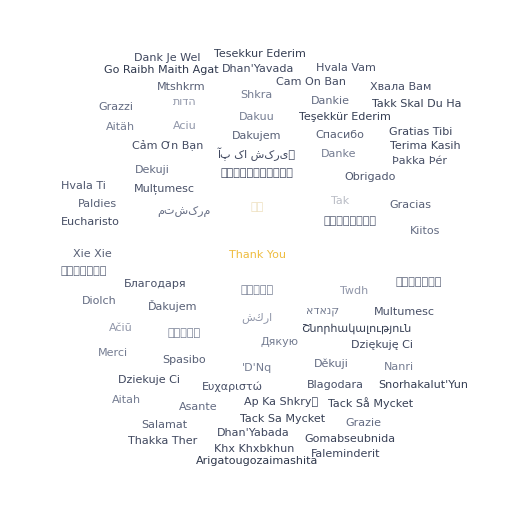

## Initialization

### Data

```mathematica
audio1=ExampleData[{"Audio","Water"}];
```

```mathematica
audio2=ExampleData[{"Audio","Walking"}];
```

```mathematica
audio3=ExampleData[{"Audio","Bird"}];
```

```mathematica
audio4=ExampleData[{"Audio","Bee"}];
```

### Style

```mathematica
SetOptions[EvaluationNotebook[],WindowTitle-> "Neural Networks And Audio"]
```